# VE401 Recitation

## About me

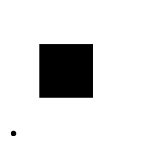

```mathematica
me=-Graphics-;
box=FindFaces[me];
HighlightImage[me,box]
```

Name: GU Zhenhao

Cell Phone: 13818175241

WeChat: GaryGZH (or you can find me using the phone number above)

E-mail: guzhenhao1@sjtu.edu.cn

Office Hour: TBD

Recitation Class: TBD

Contacting me via e-mail is preferred!

## About this Recitation Class

My recitation class aims to visualize and emphasize some key concept in class using Wolfram Mathematica, a powerful tool. It is good at plotting and famous for its intuitive interface. You are highly recommended to download and make good use of it! Steps are:

Visit https://user.wolfram.com/portal/registration.html, create a Wolfram ID with @sjtu.edu.cn email, and enter your name.

Visit https://user.wolfram.com/portal/requestAK/c51e79e5334a3600a4f740a2b3720961216dbc17 and request an activation number.

Download, enter activation number, and wait for an extension on license.

You are NOT required to understand the code. Mathematica is not mandatory in this course and the code is just for plotting and helping you to get intuitions. So don’t be afraid!

## Introduction to Probability and Counting

### Events and Mutually Exclusive Events

Intuition: Events are any subset of the sample space S. Events A_1 and A_2 are mutually exclusive if they cannot be true at the same time.

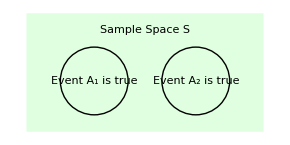

```mathematica
c = LightGreen; (* background color *)
Graphics[{c,Rectangle[{-2,-1.5},{5,2}],Black,Circle[{3,0}],Circle[],Text["Event A_1 is true",{0,0},Background->c],Text["Event A_2 is true",{3,0},Background->c],Text["Sample Space S",{1.5,1.5},Background->c]}]
```

Mathematical representation: A_1∩A_2=∅.

### Cardano’s Principle and Tree Diagrams

Intuition: The probability of an outcome A is the proportion of the ways that can lead to A, given that all the ways are equally likely and mutually exclusive.

Mathematical representation:

P[A]=(Number of ways leading to outcome A)/(number of ways the experiment can proceed)

Example: Tossing two (unbiased) coins, P[getting one head]=2/4=0.5.

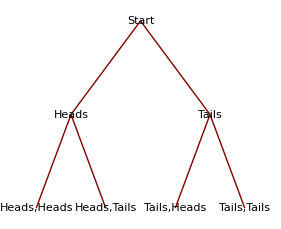

```mathematica
g={"Start"->"Heads","Start"->"Tails","Heads"->"Heads,Heads","Heads"->"Heads,Tails","Tails"->"Tails,Heads","Tails"->"Tails,Tails"};
TreePlot[g,VertexLabeling->True]
```

### Counting

The number of ways leading to outcomes is calculated using the following: with a set A={a_1,a_2,...,a_n} with n objects,

Ways of picking an object k times, allowing repetition: n^k.

Ways of choosing ordered k objects from A: (n!)/((n-k)!).

Ways of choosing unordered k objects from A: (n!)/(k!(n-k)!).

Ways of partitioning A into k subsets, A_1,...,A_k, with the number in the i^th subset is n_i: (n!)/(n_1!n_2!...n_k!).

Example:

##### Tossing a coin 4 times, what is the number of all possible outcomes?

A={heads, tails}, n=2. Total possible outcomes: 2^4=16.

##### Rolling 10 four-sided dice, what is the number of ways of getting 3 ones, 2 twos, 4 threes and 1 four?

A={1^st dice,2^nd dice,...,10^th dice} . We want to divide A into 4 subsets A_1:= dice with rolling result 1, A_2:= dice with rolling result 2, and same for A_3,A_4. In our case we need |A_1|=3, |A_2|=2, |A_3|=4, |A_4|=1, then the number of total possible ways:

```mathematica
(10!)/(3!2!4!1!)
```

12600

### Probability Measures & Spaces

Paraphrase: If a function P wants to be a probability measure, it needs to

map an event to its probability, which is in [0,1],

map the whole sample (event) space to 1, i.e. P[S]=1,

For mutually exclusive events A_1,...,A_k, P[A_1∪A_2∪...∪A_k]=P[A_1]+P[A_2]+...+P[A_k].

Properties:

P[S]=1,

P[∅]=0,

P[S\A]=1-P[A],

P[A_1∪A_2]=P[A_1]+P[A_2]-P[A_1∩A_2].

### Conditional Probability

Intuition: Given A_2 is true, the probability of A_1 is also true is the conditional probability P[A_1|A_2]. We are basically finding where A_1 is true inside the A_2 circle.

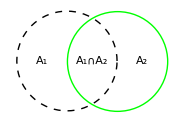

```mathematica
Graphics[{Green,Thick,Circle[{1,0}],Black,Thin,Dashed,Circle[],Text["A_1",{-0.5,0}],Text["A_2",{1.5,0}],Text["A_1∩A_2",{0.5,0}]}]
```

Mathematical representation:

P[A_1|A_2]=P[A_1∩A_2]/P[A_2]
P[A_1∩A_2]=P[A_1|A_2]P[A_2]=P[A_2|A_1]P[A_1]

### Independence

Intuition: Events A and B are independent if outcome of A does not effect outcome of B, and vice versa.

Mathematical representation:

P[A|B]=P[A]          if P[B]≠0
P[B|A]=P[B]          if P[A]≠0
P[A∩B]=P[A]P[B]     (Why?)

Summary: given events A and B, what happens to P[A∩B],P[A∪B],P[A|B],P[A|¬B] , and P[¬A|B]? You are encouraged to fill out this table by yourself first.

A and B are ... | mutually exclusive | independent
P[A∩B] |   |  
P[A∪B] |   |  
P[A|B] |   |  
P[A|¬B] |   |  
P[¬A|B] |   |

##### What does this table imply?

A and B are ... | mutually exclusive | independent
P[A∩B] | 0 | P[A]P[B] 
P[A∪B] | P[A]+P[B] | P[A]+P[B]-P[A]P[B] 
P[A|B] | 0 |  P[A]
P[A|¬B] |  P[A]/(1-P[B]) |  P[A]
P[¬A|B] | 1 | 1-P[A]

This table means if events of zero probability are excluded, mutually exclusive events are not independent and independent events are not mutually exclusive.

### Total Probability

Purpose: To write down a probability using the sum of conditional probabilities.

Mathematical representation:

P[B]=∑_(j=1)^n P[B|A_j]P[A_j]          if A_1... A_n⊂S are mutually exclusive and A_1∪...∪A_n=S

### Bayes’s Theorem

Purpose: To switch sides of a conditional probability, i.e. from P[A|B] to P[B|A].

Mathematical representation:

P[A_k|B]=P[B∩A_k]/P[B]=(P[B|A_k]P[A_k])/(P[B|A_k]P[A_k]+P[B|¬A_k]P[¬A_k])

Furthermore, if A_1... A_n⊂S are mutually exclusive and A_1∪...∪A_n=S,

P[A_k|B]=(P[B|A_k]P[A_k])/(∑_(j=1)^n P[B|A_j]P[A_j])

Example: I will recommend this video https://www.youtube.com/watch?v=HZGCoVF3YvM, which gives a nice visualization of Bayes’s theorem.

## Discrete Random Variable

### Discrete Random Variable and Probability Density Function (PDF)

Paraphrase: a discrete random variable X maps the sample space to a countable subset Ω of ℝ, with each number representing an event, and the probability density function f_X maps the subset to its probability. The PDF must follow

f_X(x) is always above zero.

The total sum of f_X(x) is equal to 1.

Note: For various distribution of random variables, we need to know its

parameter(s),

mean or expectation,

variance,

probability density function (PDF),

cumulative distribution function (CDF),

moment generating function (MGF), and

when to use it?

### Expectation

Intuition: given a set of data, what would I expect the next number to be?

Mathematical representation: for discrete random variable, E[X]=μ_X=μ=∑_(x∈Ω) x f_X(x).

Properties: for any random variable X and Y,

For a constant c∈ℝ, E[c]=c,E[c X]=c E[X],

E[X+Y]=E[X]+E[Y],

For any function φ:Ω→ℝ, E[φ∘X]=∑_(x∈Ω) φ(x) f_X(x).

##### What do these properties imply?

E[·] is a linear operation!

### Variance and Standard Variance

Intuition: how much does random variable deviate from the mean?

Mathematical representation:

Variance: Var[X]=σ_X^2=σ^2=E[(X-E[X])]^2=E[X^2]-E[X]^2.

Standard variance: σ_X=√Var[X].

Properties:

For a constant c∈ℝ, Var[c]=0,Var[c X]=c^2 Var[X].

For independent random variable X and Y, Var[X+Y]=Var[X]+Var[Y].

### Moment and Moment Generating Function (MGF)

Intuition: MGF encodes the sequence of all moments, E[X^0],E[X^1],E[X^2],... into one function.

Mathematical representation: MGF exists iff E[e^(t X)] exists, in which case

m_X(t)=∑_(k=0)^∞ E[X^k]/(k!)t^k=E[e^(t X)]

and the k^th moment can be calculated using E[X^k]=((d^k m_X(t))/(d t^k))_(t=0) .

Properties: if random variable X and Y has MGF,

If two distributions have same MGF, then two distributions are identical. i.e.  ∀_(t∈(-ε,ε))m_X(t)=m_Y(t)⇒∀_(x∈Ω)f_X(x)=f_Y(x).

Linear transformation: for any constant α,β∈ℝ, m_(α X+β)(t)=e^(β t)m_X(α t). (Ve401 slide 281)

Linear combination: let X_1 and X_2 be two independent random variable and Y=X_1+X_2, then m_Y=m_X_1 m_X_2. (Ve401 slide 280)

### Cumulative Distribution Function (CDF)

Mathematical representation: F_X(x):=P[X≤x]=∑_(y≤x) f_X(y).

### Bernoulli Random Variable

Purpose: the probability of success in 1 trial?

Parameter and properties:

p∈[0,1], describing the probability of success.

Mean | p
Variance | p(1-p)
PDF | Piecewise[{{1-p, x==0}, {p, x==1}, {0, otherwise}}]
CDF | Piecewise[{{0, x<0}, {1-p, 0≤x<1}, {1, otherwise}}]
MGF | 1-p+e^t p

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[BernoulliDistribution[p],x],{x,0,1},
PlotRange->{0,1},
AxesOrigin->{-.1,0},
AxesLabel->{"x","P[x]"},
PlotLabel->"PDF of Bernoulli Distribution with p="<>ToString[p]
],{p,0,1},Paneled->False]
```

### Binomial Random Variable

Purpose: how many successes in n trial(s)?

Parameter and properties:

p∈[0,1], describing the probability of success in each trial.

n∈{0,1,2,...} is the number of trials.

Mean | n p
Variance | n (1-p) p
PDF | Piecewise[{{Binomial[n, x] p^x (1-p)^(n-x), 0≤x≤n}, {0, otherwise}}]
CDF | Piecewise[{{∑_(y=0)^Floor[x] Binomial[n, x] p^x (1-p)^(n-x), 0≤x<n}, {1, x≥n}}]
MGF | (p (e^x-1)+1)^n

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[BinomialDistribution[n,p],x],{x,0,n},
PlotRange->{0,1},
AxesOrigin->{-0.1 n,0},
AxesLabel->{"x","P[x]" },
PlotLabel->"PDF of Binomial Distribution with p="<>ToString[p]<>", n="<>ToString[n]
],{p,0,1},{n,{1,5,10,15,20}},Paneled->False]
```

### Geometric Random Variable

Purpose: how many trials until first success?

Parameter and properties:

p∈[0,1], describing the probability of success in each trial.

n∈{0,1,2,...} is the number of trials.

Mean | n p
Variance | n (1-p) p
PDF | Piecewise[{{(1-p)^(x-1) p, x≥1}, {0, otherwise}}]
CDF | Piecewise[{{1-(1-p)^Floor[x], x≥1}, {0, otherwise}}]
MGF | p/(1-(1-p) e^(x-1))

```mathematica
(* Plot of PDF *)
Manipulate[
DiscretePlot[
PDF[GeometricDistribution[p],x-1],{x,1,10},
PlotRange->{0,1},
AxesOrigin->{0,0},
AxesLabel->{"x","P[x]" },
PlotLabel->"PDF of Geometric Distribution with p="<>ToString[p]
],{p,0.001,1},Paneled->False]
```